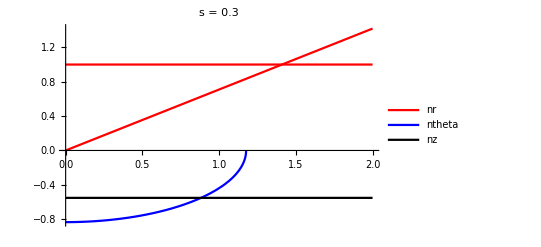

-0.536784+0. ⅈ

```mathematica
ClearAll["Global`*"]
nr[u_,s_] :=(1+2s)/(√(1+4 *s+4 *s^2+9 *s^2 (u)^2));
nz[u_,s_]:=(-3 s *u)/(√(1+4 *s+4 *s^2+9 *s^2 (u)^2));
Simplify[nr[u,s]^2 + nz[u,s]^2];
s = .3;
title = StringJoin["s = ",ToString[s]];
Plot[{nr[u,s],nz[u,s]},{u,0,10},PlotStyle->{{Red},{Black}},PlotLegends->{Style[nr, 16],Style[nz,16]},PlotLabel->Style[title,14]];
Plot[ArcTan[nz[u,s]/nr[u,s]],{u,0,1}];
nrad[u_,s_] :=(u*3*s* √(1-s))/(√(2+s) (1-s));
nthet[u_,s_]:= -(√(-1-s+2 s^2+9 (s^2)*(u)^2))/(√(-2 +s+s^2));
nzet[s_]:= -(√(1-s))/(√(2+s));
Simplify[(nrad[u,s])^2 + (nthet[u,s])^2 + (nzet[s])^2];
Plot[{nrad[u,s],nthet[u,s],nzet[s],(nrad[u,s])^2 + (nthet[u,s])^2 + (nzet[s])^2},{u,0,2}, PlotStyle->{{Red},{Blue}, {Black}},PlotLegends->{Style[nr, 16],Style[ntheta,16],Style[nz,16]},PlotLabel->Style[title,14]]
Clear[s,u]
Simplify[Sqrt[(-1-s+2s^2)/(-2+s+s^2)]];
nthet[.9,.3]
```